# Hitting of Cyclones to West Coast North America

Baoxiang Pan
7.10.2017

## Import Lagrangian Detected Cyclone Data

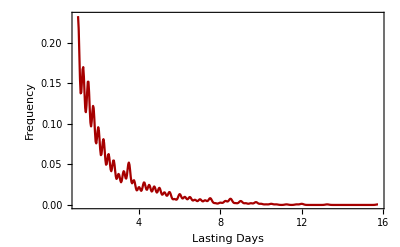

```mathematica
cyclones=Import["/Users/lambda/Documents/Data/Cyclones/ncepstorms_2009.txt","Table"];
data=Table[Select[cyclones,#[[-1]]==i&],{i,Max[Map[#[[-1]]&,cyclones]]}];
length=Map[Length,data]*0.25;
Block[{distribution=SmoothKernelDistribution[length]},
Plot[PDF[distribution, x], {x, 1, Max[length]},
	PlotRange->Full,
	BaseStyle->18,
	Frame->True,
	FrameLabel->{"Lasting Days","Frequency"}]]
```

```mathematica
cyclones=Import["/Users/lambda/Documents/Data/Cyclones/cyclones.txt","Table"][[2;;]];
```

```mathematica
Table[Block[{filename="ncepstorms_19"<>ToString[i]<>".txt"},
	Export[filename,Select[cyclones,#[[3]]==i&],"Table"]],{i,58,99}];
```

```mathematica
Table[Block[{filename="ncepstorms_200"<>ToString[i]<>".txt"},
	Export[filename,Select[cyclones,#[[3]]==i&],"Table"]],{i,0,8}];
```

```mathematica
CycloneSpecify[time_,range_]:=Block[{file="ncepstorms_"<>ToString[time[[1]]]<>".txt",
			lag=3,cyclones,s1,s2,ByPass},
	SetDirectory["/Users/lambda/Documents/Data/Cyclones"];
	cyclones=Import[file,"Table"];
	s1=Select[cyclones,Abs[DateDifference[If[#[[3]]<20,
							DateObject[{2000+#[[3]],#[[4]],#[[5]]},"Day", "Gregorian", -6.],
							DateObject[{1900+#[[3]],#[[4]],#[[5]]},"Day", "Gregorian", -6.]],
							DateObject[time,"Day","Gregorian",-6.]][[1]]]<lag&];
	s2=Table[Select[s1,#[[-1]]==i&],{i,Max[Map[#[[-1]]&,s1]]}];
	ByPass[track_]:=Block[{InOrNot},
	    InOrNot[point_]:=And[point[[1]]>=range[[1,1]],point[[1]]<range[[1,2]],
	                       point[[2]]>=range[[2,1]],point[[2]]<range[[2,2]]];
		Map[InOrNot[{#[[14]],#[[15]]}]&,track]/.List->Or];
	Select[s2,ByPass]]
```

```mathematica
SequentialDetection[date_]:=Block[{pendant=Table[i,{i,2,365,5}]},
	Map[CycloneSpecify[DatePlus[DateObject[date,"Day", "Gregorian", -6.],{#,"Day"}][[1]],
				  {{30,70},{219,251}}]&,pendant]]
```

```mathematica
test=SequentialDetection[{1958,1,1}];
```